```mathematica
f[x_] := 1/(1+E^(-x))
```

```mathematica
f[1]
```

1/(1+1/ⅇ)

```mathematica
N[1/(1+1/ⅇ)]
```

0.731059

```mathematica
f[1.9]
```

0.869892

```mathematica
NumberForm[0.8698915256370021,16]
```

0.869891525637002

```mathematica
f'[1]
```

1/((1+1/ⅇ)^2 ⅇ)

```mathematica
N[1/((1+1/ⅇ)^2 ⅇ)]
```

0.196612

```mathematica
f''[1]
```

2/((1+1/ⅇ)^3 ⅇ^2)-1/((1+1/ⅇ)^2 ⅇ)

```mathematica
N[2/((1+1/ⅇ)^3 ⅇ^2)-1/((1+1/ⅇ)^2 ⅇ)]
```

-0.0908577

```mathematica
N[f[1]]
```

0.731059

```mathematica
N[f'[1]]
```

0.196612

```mathematica
N[f''[1]]
```

-0.0908577

```mathematica
f[1]*(1-f[1])
```

(1-1/(1+1/ⅇ))/(1+1/ⅇ)

```mathematica
N[(1-1/(1+1/ⅇ))/(1+1/ⅇ)]
```

0.196612

```mathematica
0.19661193324148185*(1-0.19661193324148185)
```

0.157956

```mathematica
ioPaar={{{0.9,0.9,0.9,0.9,0.1,0.1,0.9,0.9,0.9},{0.1}},{{0.9,0.9,0.9,0.1,0.9,0.1,0.1,0.9,0.1},{0.9}},{{0.9,0.9,0.9,0.9,0.1,0.9,0.9,0.1,0.9},{0.1}},{{0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1,0.9},{0.9}},{{0.9,0.9,0.9,0.1,0.1,0.9,0.9,0.9,0.9},{0.1}},{{0.1,0.9,0.1,0.1,0.9,0.1,0.9,0.9,0.9},{0.9}},{{0.9,0.1,0.9,0.9,0.1,0.9,0.9,0.9,0.9},{0.1}},{{0.9,0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1},{0.9}}};
ioPaar[[8]]
{{0.9,0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1},{0.9}}
inzahl=9;hidzahl=3;outzahl=1;
wh=Table[Table[Random[Real,{-0.1,0.1}],{inzahl}],{hidzahl}];
wo=Table[Table[Random[Real,{-0.1,0.1}],{hidzahl}],{outzahl}];
eta=0.5;
TRAININGSPHASE:iter=5000;sigmoid[x_]:=1/(1+Exp[-x]);
(*y=w.in;*)
Fehlerliste=Table[{in,t}=ioPaar[[Random[Integer,{1,8}]]];
outhid=sigmoid[wh.in];
out=sigmoid[wo.outhid];
(*e=t-y;*)e=t-out;
outdelta=e out(1-out);
hiddelta=outhid(1-outhid) Transpose[wo].outdelta;
```

{{0.9,0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1},{0.9}}

{{0.9,0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1},{0.9}}

```mathematica
ioPaar={{{0.9,0.9,0.9,0.9,0.1,0.1,0.9,0.9,0.9},{0.1,0.1}},{{0.9,0.9,0.9,0.1,0.9,0.1,0.1,0.9,0.1},{0.9,0.1}},{{0.9,0.9,0.9,0.9,0.1,0.9,0.9,0.1,0.9},{0.1,0.1}},{{0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1,0.9},{0.9,0.1}},{{0.9,0.9,0.9,0.1,0.1,0.9,0.9,0.9,0.9},{0.1,0.1}},{{0.1,0.9,0.1,0.1,0.9,0.1,0.9,0.9,0.9},{0.9,0.1}},{{0.9,0.1,0.9,0.9,0.1,0.9,0.9,0.9,0.9},{0.1,0.1}},{{0.9,0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1},{0.9,0.1}}};
```

```mathematica
ioPaar[[8]]
```

{{0.9,0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1},{0.9,0.1}}

```mathematica
inzahl=9;hidzahl=3;outzahl=2;
```

```mathematica
wh=Table[Table[Random[Real,{-0.1,0.1}],{inzahl}],{hidzahl}];
wo=Table[Table[Random[Real,{-0.1,0.1}],{hidzahl}],{outzahl}];
eta=0.5;
```

```mathematica
iter=1000;sigmoid[x_]:=1/(1+Exp[-x]);
(*y=w.in;*)
```

```mathematica
Fehlerliste=Table[{in,t}=ioPaar[[Random[Integer,{1,8}]]];
outhid=sigmoid[wh.in];
out=sigmoid[wo.outhid];
(*e=t-y;*)
e=t-out;
outdelta=e out(1-out);
hiddelta=outhid(1-outhid) Transpose[wo].outdelta;
(*w+=eta e in;*)wo+=eta Outer[Times,outdelta,outhid];
wh+=eta Outer[Times,hiddelta,in];
{e.e,wo,wh},{k,1,iter}];
```

```mathematica
outdelta
```

{-0.0130237,-0.000157872}

0.27034

```mathematica
{-0.9929045511683615,1.513158869470985,-0.6809071731372235}
```

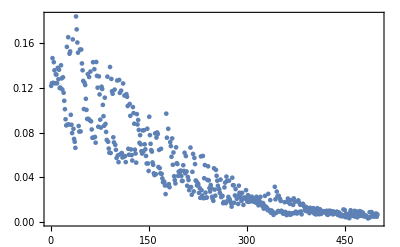

```mathematica
ListPlot[Fehlerliste[[All,1]],Frame->True,PlotRange->All]
```

```mathematica
in=ioPaar[[8,1]];
outhid=sigmoid[wh.in];
out=sigmoid[wo.outhid]
{0.899976}
```

{0.551018}

{0.899976}

```mathematica
input = {1,2,3,4}
```

{1,2,3,4}